```mathematica
SetDirectory["/Users/BACCH-SP-1b/Programming/smooth"];
```

```mathematica
link = Install["/Users/BACCH-SP-1b/Programming/smooth/realOctaveSmooth"]
```

LinkObject[/Users/BACCH-SP-1b/Programming/smooth/realOctaveSmooth,998,12]

```mathematica
LinkPatterns[link]
```

{RealOctaveSmooth[fractionDenominator_Real,windowType_Integer,data_List]}

```mathematica
?RealOctaveSmooth
```

RealOctaveSmooth[N, oSwindowType, data] applies a 1/Nth octave smoothing filter to data using a window (0 for rectangular, otherwise Hanning).

### Needs example C11Rough, and BACCH Routines

```mathematica
C11Smooth = RealOctaveSmooth[N[12],1,C11Rough];
```

```mathematica
AbsoluteTiming[C11Smooth = RealOctaveSmooth[N[12],1,C11Rough];]
AbsoluteTiming[C11OldSmooth = octaveSmooth[C11Rough,12,1];]
```

{0.01101,Null}

{0.078409,Null}

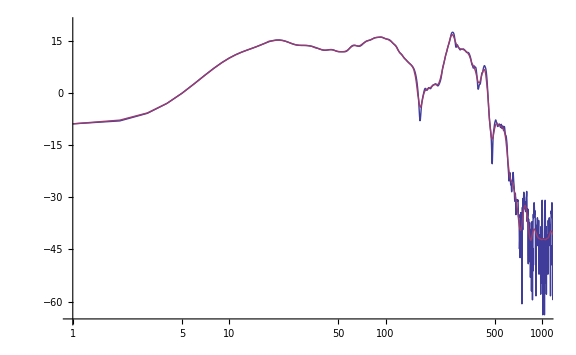

```mathematica
ListLogLinearPlot[{C11Rough,C11Smooth},Joined->True,ImageSize->Large,PlotRange->{{1,1024},{-65,20}}]
```

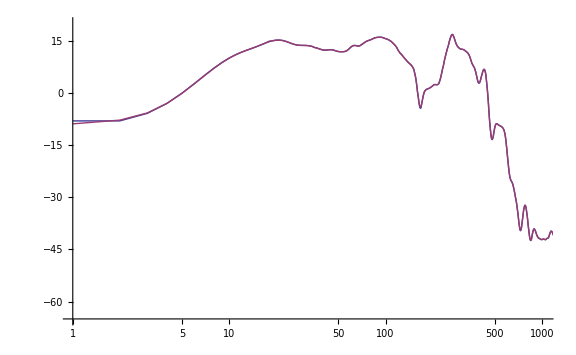

```mathematica
ListLogLinearPlot[{C11OldSmooth,C11Smooth},Joined->True,ImageSize->Large,PlotRange->{{1,1024},{-65,20}}]
```

### Wrapping Function:

```mathematica
octaveSmooth[data_,frac_,oSwindowType_]:=RealOctaveSmooth[N[frac],Round[oSwindowType],data]
```